```mathematica
cities={Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"SanDiego","California","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}],
Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"SaltLakeCity","Utah","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}],
Entity["City",{"Denver","Colorado","UnitedStates"}],Entity["City",{"Boulder","Colorado","UnitedStates"}]};
```

```mathematica
travelprices={343,612,221,279,784,709,221,1129,529,529};
```

```mathematica
distances=GeoDistance[Here,#]&/@cities
```

{917.799 mi,2251.49 mi,183.67 mi,585.354 mi,2322.43 mi,1837.7 mi,385.148 mi,4830.73 mi,1471.26 mi,1500.47 mi}

```mathematica
travelassociation=AssociationThread[cities->Transpose[{distances,travelprices}]]
```

<|Miami→{917.799 mi,343},San Diego→{2251.49 mi,612},New York City→{183.67 mi,221},Chicago→{585.354 mi,279},Seattle→{2322.43 mi,784},Salt Lake City→{1837.7 mi,709},Boston→{385.148 mi,221},Honolulu→{4830.73 mi,1129},Denver→{1471.26 mi,529},Boulder→{1500.47 mi,529}|>

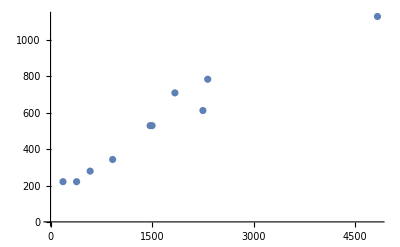

```mathematica
ListPlot[Tooltip[travelassociation[#],#]&/@cities]
```

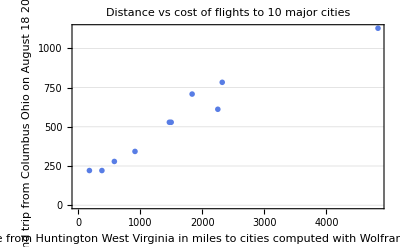

```mathematica
ListPlot[Tooltip[travelassociation[#],#["Name"]]&/@cities,FrameLabel->{"Geodesic Distance from Huntington West Virginia in miles to cities computed with Wolfram Mathematica GeoDistance","Cost of cheapest round trip from Columbus Ohio on August 18 2022 from Google Flights"},LabelStyle->Directive[16,FontFamily->"JetBrains Mono"],Frame->True,ImageSize->Full,PlotTheme->"Business",PlotLabel->"Distance vs cost of flights to 10 major cities"]
```

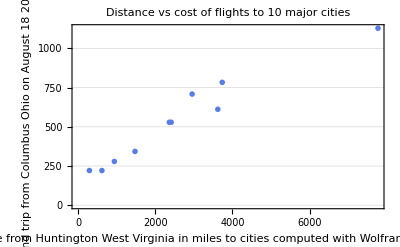

```mathematica
Block[{cities,travelAssociation},cities={Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"SanDiego","California","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}],
Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"SaltLakeCity","Utah","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}],
Entity["City",{"Denver","Colorado","UnitedStates"}],Entity["City",{"Boulder","Colorado","UnitedStates"}]};travelAssociation=AssociationThread[cities->Transpose[{GeoDistance[Here,#,UnitSystem->"Metric"]&/@cities,{343,612,221,279,784,709,221,1129,529,529}}]];ListPlot[Tooltip[travelAssociation[#],#["Name"]]&/@cities,FrameLabel->{"Geodesic Distance from Huntington West Virginia in miles to cities computed with Wolfram Mathematica GeoDistance","Cost of cheapest round trip from Columbus Ohio on August 18 2022 from Google Flights"},LabelStyle->Directive[16,FontFamily->"JetBrains Mono"],Frame->True,ImageSize->Full,PlotTheme->"Business",PlotLabel->"Distance vs cost of flights to 10 major cities"]]
```

```mathematica
travelprices={343,612,221,279,784,709,221,1129,529,529};
```

```mathematica
distances=GeoDistance[Here,#]&/@cities
```

{917.799 mi,2251.49 mi,183.67 mi,585.354 mi,2322.43 mi,1837.7 mi,385.148 mi,4830.73 mi,1471.26 mi,1500.47 mi}

```mathematica
travelassociation=AssociationThread[cities->Transpose[{distances,travelprices}]]
```

<|Miami→{917.799 mi,343},San Diego→{2251.49 mi,612},New York City→{183.67 mi,221},Chicago→{585.354 mi,279},Seattle→{2322.43 mi,784},Salt Lake City→{1837.7 mi,709},Boston→{385.148 mi,221},Honolulu→{4830.73 mi,1129},Denver→{1471.26 mi,529},Boulder→{1500.47 mi,529}|>

```mathematica
ClearAll[travelprices,travelassociation,cities,distances]
```

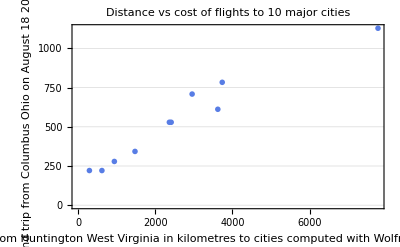

```mathematica
Block[{cities,travelAssociation},cities={Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"SanDiego","California","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}],
Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"SaltLakeCity","Utah","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}],
Entity["City",{"Denver","Colorado","UnitedStates"}],Entity["City",{"Boulder","Colorado","UnitedStates"}]};travelAssociation=AssociationThread[cities->Transpose[{GeoDistance[Here,#,UnitSystem->"Metric"]&/@cities,{343,612,221,279,784,709,221,1129,529,529}}]];ListPlot[Tooltip[travelAssociation[#],#["Name"]]&/@cities,FrameLabel->{"Geodesic Distance from Huntington West Virginia in kilometres to cities computed with Wolfram Mathematica GeoDistance","Cost of cheapest round trip from Columbus Ohio on August 18 2022 from Google Flights"},LabelStyle->Directive[16,FontFamily->"JetBrains Mono"],Frame->True,ImageSize->Full,PlotTheme->"Business",PlotLabel->"Distance vs cost of flights to 10 major cities"]]
```

```mathematica
Block[{cities,travelAssociation},cities={Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"SanDiego","California","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}],
Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"SaltLakeCity","Utah","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}],
Entity["City",{"Denver","Colorado","UnitedStates"}],Entity["City",{"Boulder","Colorado","UnitedStates"}]};travelAssociation=AssociationThread[cities->Transpose[{GeoDistance[Here,#]&/@cities,{343,612,221,279,784,709,221,1129,529,529}}]];ListPlot[Tooltip[travelAssociation[#],#["Name"]]&/@cities,FrameLabel->{"Geodesic Distance from Huntington West Virginia in miles to cities computed with Wolfram Mathematica GeoDistance","Cost of cheapest round trip from Columbus Ohio on August 18 2022 from Google Flights"},LabelStyle->Directive[16,FontFamily->"JetBrains Mono"],Frame->True,ImageSize->Full,PlotTheme->"Business",PlotLabel->"Distance vs cost of flights to 10 major cities"]]
```

-Graphics-